Time for one eigenvalue/eigensystem evaluation 0.000791478

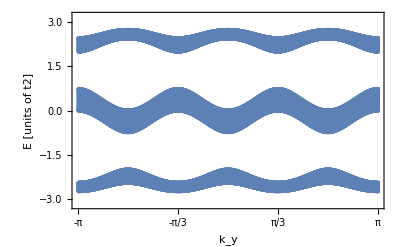

```mathematica
Begin["OBC`"];
ClearAll["OBC`*"];

a=1; (*Unit of length*)
t=1; (*For t≠1, the edge states for finite N have an avoided crossing*)

α=1/3;
Q=If[α>0,Denominator[Rationalize[α]], 1];

PBC=True; (* PBC or OBC? *)

(*Study of edge states*)
edgeStudy=False;

(* Numbers of cells *)
Ncx=50; (*40*)
Ncy=420; (*300*)(*Should be divisible by 6, in order to get the points where edge states are degenerate*)
(* Numbers of atoms *)
Nax=Q Ncx;
Nay=Ncy;

(*Define NULL matrices*)
En=Table[0,{m,1,Nay},{l,1,Nax}];
vv=Table[0,{m,1,Nay},{l,1,Nax}];

(* Points of the BZ along y *)
time=Timing[
For[m=1, m≤ Nay, m++,ky = -π+2π  m/Nay;  

ClearAll[i,j];
Hmatrix= Normal[SparseArray[
{
{i_,j_}/;Abs[i-j]==1 ->t,
{i_,j_}/;Abs[i-j]==0 ->2 Cos[ky a-2 Pi α i]
}
,{Nax,Nax},0]];

If[PBC,
Hmatrix[[1,Nax]]=Hmatrix[[Nax,1]]=t;
];

eigen=Transpose[Sort[Transpose[Eigensystem[N[Hmatrix]]],#1[[1]]<#2[[1]] &]];

(*1d energy bands*)
For[l=1,l≤Nax,l++,
En[[m,l]]= eigen[[1,l]];
vv[[m,l]]=eigen[[2,l]] ;
] 

] (* Cycle on BZ CLOSING *)
];

Print["\nTime for one eigenvalue/eigensystem evaluation ", time[[1]]/(Nax*Nay)]

(*Plot of energy bands with colors for α=1/3*)
Show[
Table[
ListPlot[Table[{-π+2π  m/Nay,En[[m,l]]}, {m,1,Nay}],PlotRange->{{-Pi,Pi},{-3.2,3.2}}],{l,1,Nax}
], Frame->True, FrameLabel->{"k_y","E [units of t2]"},Axes->False,FrameTicks->{  {Automatic,None} ,{{-Pi,-2Pi/3,-Pi/3,0,Pi/3,2 Pi/3, Pi},None}  }
]


(*(*Plot of energy bands with colors for α=1/4*)
Show[
Table[
ListPlot[Table[{-π+2π  m/Nay,En[[m,l]]}, {m,1,Nay}],PlotRange->{{-Pi,Pi},{-3.2,3.2}},PlotStyle->Black],{l,1,Ncx}
],Table[
ListPlot[Table[{-π+2π  m/Nay,En[[m,l]]}, {m,1,Nay}],PlotRange->{{-Pi,Pi},{-3.2,3.2}},PlotStyle->Black],{l,Ncx+1,2Ncx}
],Table[
ListPlot[Table[{-π+2π  m/Nay,En[[m,l]]}, {m,1,Nay}],PlotRange->{{-Pi,Pi},{-3.2,3.2}},PlotStyle->Black],{l,2Ncx+1,3Ncx}
],Table[
ListPlot[Table[{-π+2π  m/Nay,En[[m,l]]}, {m,1,Nay}],PlotRange->{{-Pi,Pi},{-3.2,3.2}},PlotStyle->Black],{l,3Ncx+1,4Ncx}
], Frame->True, FrameLabel->{"k_y","E [units of t2]"},Axes->False,FrameTicks->{  {Automatic,None} ,{{-Pi,-2Pi/3,-Pi/3,0,Pi/3,2 Pi/3, Pi},None}  }
]*)



(*Points of degeneracy of the edge states, for t=1*)

(*Each of the three "bands" has the same number of state. Thus the position of edge states could be predicted a priori*)

If[edgeStudy,

indecesL={}; (*positions of edge states at ky<0*)

For[l=1,l≤Nax,l++,
If[-2<En[[Nay/6,l]]<-1,AppendTo[indecesL,l]];
]
indecesL
En[[Nay/6,indecesL[[1]]]]
En[[Nay/6,indecesL[[2]]]]


indecesR={}; (*positions of edge states at ky>0*)

For[l=1,l≤Nax,l++,
If[1<En[[2 Nay/3,l]]<2,AppendTo[indecesR,l]];
]
indecesR
En[[2 Nay/3,indecesR[[1]]]]
En[[2 Nay/3,indecesR[[2]]]]



(*Edge states 1d dispersion relation*)
dispEdge1=Table[{-π+2π  m/Nay,En[[m,indecesL[[1]]]]}, {m,1,Nay}];
dispEdge2=Table[{-π+2π  m/Nay,En[[m,indecesL[[2]]]]}, {m,1,Nay}];
dispEdge3=Table[{-π+2π  m/Nay,En[[m,indecesR[[1]]]]}, {m,1,Nay}];
dispEdge4=Table[{-π+2π  m/Nay,En[[m,indecesR[[2]]]]}, {m,1,Nay}];

p1=ListPlot[dispEdge1,Joined->True];
p2=ListPlot[dispEdge2,Joined->True];
p3=ListPlot[dispEdge3,Joined->True];
p4=ListPlot[dispEdge4,Joined->True];


Show[{p1,p2,p3,p4},PlotRange->{{-Pi,Pi},{-3.2,3.2}}, Frame->True, FrameLabel->{"k_y","E"},Axes->False,FrameTicks->{  {Automatic,None} ,{{-Pi,-2Pi/3,-Pi/3,0,Pi/3,2 Pi/3, Pi},None}  },Joined->True]



(*Offset*)
δ=50;

Print["\nEdge states corresponding to IndecesR"]

Print["\nHigher energy edge state"]

Print["\nOffset -2δ"]
ListPlot[ Table[  {m,vv[[2 Nay/3-2δ,indecesR[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nOffset -δ"]
ListPlot[ Table[  {m,vv[[2 Nay/3-δ,indecesR[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nNo offset: ky=Pi/3"]
ListPlot[ Table[  {m,vv[[2 Nay/3,indecesR[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nOffset δ"]
ListPlot[ Table[  {m,vv[[2 Nay/3+δ,indecesR[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nOffset 2δ"]
ListPlot[ Table[  {m,vv[[2 Nay/3+2δ,indecesR[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]



Print["\nLower energy edge state"]

Print["\nOffset -2δ"]
ListPlot[ Table[  {m,vv[[2 Nay/3-2δ,indecesR[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nOffset -δ"]
ListPlot[ Table[  {m,vv[[2 Nay/3-δ,indecesR[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nNo offset: ky=Pi/3"]
ListPlot[ Table[  {m,vv[[2 Nay/3,indecesR[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nOffset δ"]
ListPlot[ Table[  {m,vv[[2 Nay/3+δ,indecesR[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nOffset 2δ"]
ListPlot[ Table[  {m,vv[[2 Nay/3+2δ,indecesR[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]




Print["\nDistribution R; blue Left weigths, red Right weights"]

Print["\nUpper energy edge state"]
Show[
ListPlot[Table[{-π+2π  m/Nay,(vv[[m,indecesR[[2]],1] ])^2+(vv[[m,indecesR[[2]],2] ])^2}, {m,1,Nay}],Joined->True,PlotStyle->Blue],
ListPlot[Table[{-π+2π  m/Nay,(vv[[m,indecesR[[2]],Nax] ])^2+(vv[[m,indecesR[[2]],Nax-1] ])^2}, {m,1,Nay}],Joined->True,PlotStyle->Red]
]

Print["\nLower energy edge state"]
Show[
ListPlot[Table[{-π+2π  m/Nay,(vv[[m,indecesR[[1]],1] ])^2+(vv[[m,indecesR[[1]],2] ])^2}, {m,1,Nay}],Joined->True,PlotStyle->Blue,PlotRange->All],
ListPlot[Table[{-π+2π  m/Nay,(vv[[m,indecesR[[1]],Nax] ])^2+(vv[[m,indecesR[[1]],Nax-1] ])^2}, {m,1,Nay}],Joined->True,PlotStyle->Red,PlotRange->All]
]


(*Print["\nEdge states corresponding to IndecesL"]

(*Edge states for ky=-2Pi/3, i.e. m=Nay/6*)
Print["\nNo offset: ky=-2Pi/3"]
ListPlot[ Table[  {m,vv[[Nay/6,indecesL[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]
ListPlot[ Table[  {m,vv[[Nay/6,indecesL[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]


Print["\nOffset δ, R"]
ListPlot[ Table[  {m,vv[[Nay/6+δ,indecesL[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]
ListPlot[ Table[  {m,vv[[Nay/6+δ,indecesL[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nOffset -δ, R"]
ListPlot[ Table[  {m,vv[[Nay/6-δ,indecesL[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]
ListPlot[ Table[  {m,vv[[Nay/6-δ,indecesL[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nOffset 2δ, R"]
ListPlot[ Table[  {m,vv[[Nay/6+2δ,indecesL[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]
ListPlot[ Table[  {m,vv[[Nay/6+2δ,indecesL[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nOffset -2δ, R"]
ListPlot[ Table[  {m,vv[[Nay/6-2δ,indecesL[[2]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]
ListPlot[ Table[  {m,vv[[Nay/6-2δ,indecesL[[1]],m] ]},{m,1,Nax}],Joined->True,PlotRange->All]

Print["\nDistribution L"]
ListPlot[Table[{-π+2π  m/Nay,(vv[[m,indecesL[[2]],1] ])^2+(vv[[m,indecesL[[2]],2] ])^2+(vv[[m,indecesL[[2]],Nax] ])^2+(vv[[m,indecesL[[2]],Nax-1] ])^2}, {m,1,Nay}],Joined->True]
ListPlot[Table[{-π+2π  m/Nay,(vv[[m,indecesL[[1]],1] ])^2+(vv[[m,indecesL[[1]],2] ])^2+(vv[[m,indecesL[[1]],Nax] ])^2+(vv[[m,indecesL[[1]],Nax-1] ])^2}, {m,1,Nay}],Joined->True]
*)


]




End[];
```